## 3.029 Data-Viz Hour 02/24/2022

Scientific Data Link:

https://www.nature.com/articles/sdata20159

## Elastic Properties of Inorganic Compounds

Downloaded raw dataset from: https://doi.org/10.5061/dryad.h505v

Extracted `ec.json` file in my Downloads folder

### Importing and Inspecting Data

Import as an association

```mathematica
rawData=Import["/home/george/Downloads/ec.json","RawJSON"];
```

Check dimensions of dataset

```mathematica
rawData//Dimensions
```

{1181}

It’s a list of associations for 1181 inorganic compounds

```mathematica
Head/@rawData[[;;2]]
```

{Association,Association}

Inspecting keys for first inorganic compound

```mathematica
Keys[rawData[[1]]]
```

{G_Reuss,G_VRH,G_Voigt,K_Reuss,K_VRH,K_Voigt,compliance_tensor,elastic_anisotropy,elastic_tensor,elastic_tensor_original,formula,kpoint_density,material_id,nsites,poisson_ratio,poscar,space_group,structure,volume}

Not all headings are self-explanatory

Go back to journal article and see longer descriptions

elastic_tensor

stiffness tensor, C_IJ

Note: only two indices since it’s using Voight notation

1 → 11

2 → 22

3 → 33

4 → 23, 32

5 → 13, 31

6 → 12, 21

elastic_tensor_original

stiffness tensor in “primitive-cell” orientation

often more convenient to do calculation in this orientation

we will ignore this

compliance_tensor, s_IJ

poisson_ratio

“Isotropic” Poisson ratio, ν

K_Voight

“Bulk modulus” according to Voigt’s formula (upper bound)

Let’s check this formula

```mathematica
With[{c=rawData[[1,"elastic_tensor"]]},
((c[[1,1]]+c[[2,2]]+c[[3,3]])+2(c[[1,2]]+c[[2,3]]+c[[3,1]]))/9
]
```

194.27

```mathematica
rawData[[1,"K_Voigt"]]
```

194.27

K_Reuss (lower bound)

```mathematica
rawData[[1,"K_Reuss"]]
```

194.268

This is interesting, the bound for the first compound - appears to be very narrow

Is this true for all materials?

```mathematica
Short[#["K_Reuss"]&/@rawData]
```

{194.268,«1179»,35.9387}

```mathematica
Short[Lookup[rawData,"K_Reuss"]]
```

{194.268,«1179»,35.9387}

```mathematica
Short[rawData[[All,"K_Reuss"]]]
```

{194.268,«1179»,35.9387}

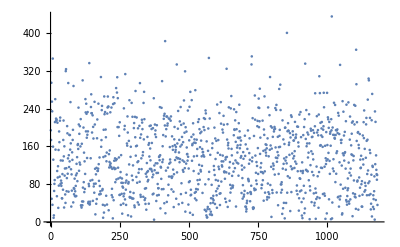

```mathematica
ListPlot[Lookup[rawData,"K_Reuss"]]
```

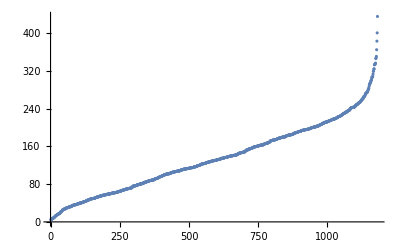

```mathematica
ListPlot[Sort[Lookup[rawData,"K_Reuss"]],Frame->All]
```

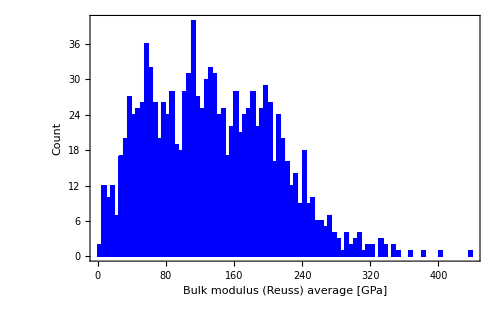

```mathematica
Histogram[Lookup[rawData,"K_Reuss"],100,"Count",Frame->True,FrameLabel->{"Bulk modulus (Reuss) average [GPa]","Count"},ChartStyle->Blue,ImageSize->500,
LabelStyle->Directive[18,Black]]
```

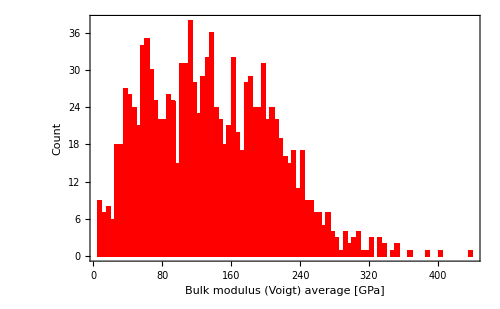

```mathematica
Histogram[Lookup[rawData,"K_Voigt"],100,"Count",Frame->True,FrameLabel->{"Bulk modulus (Voigt) average [GPa]","Count"},ChartStyle->Red,ImageSize->500,
LabelStyle->Directive[18,Black]]
```

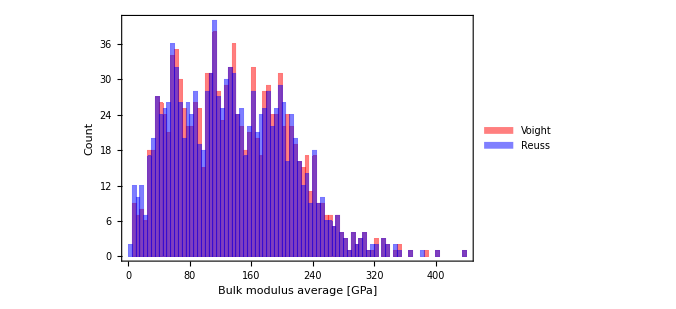

```mathematica
Histogram[Transpose[Lookup[rawData,{"K_Voigt","K_Reuss"}]],100,"Count",Frame->True,FrameLabel->{"Bulk modulus average [GPa]","Count"},ChartStyle->{Red,Blue},ImageSize->500,
LabelStyle->Directive[18,Black],ChartLegends->Placed[{"Voight","Reuss"},{0.75,0.75}]]
```

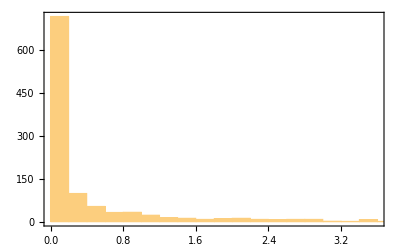

```mathematica
Histogram[Subtract[#1,#2]/Mean[{#1,#2}] 100&@@@Lookup[rawData,{"K_Voigt","K_Reuss"}],Frame->True]
```

```mathematica
Simplify[(kv-Mean[{kv,kr}])/Mean[{kv,kr}]]
```

(-kr+kv)/(kr+kv)

```mathematica
normalizedDeviation=ReverseSort[(#2-#1)/(#2+#1)100.&@@@Lookup[rawData,{"K_Reuss","K_Voigt"}]];
```

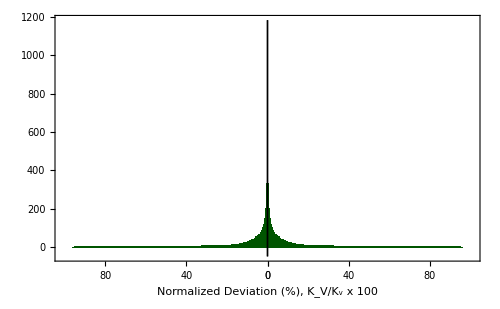

```mathematica
PairedBarChart[normalizedDeviation,normalizedDeviation,BarSpacing->{0,0,0},Frame->True,PerformanceGoal->"Speed",ImageSize->500,BaseStyle->18,ChartStyle->RGBColor[0,1/3,0],LabelStyle->Black,FrameTicks->{Automatic,None},FrameLabel->{"Normalized Deviation (%), K_V/K_v x 100",None}]
```